```mathematica
(* Exercício 1 *)
A={
{1,0,-1},
{0,2,3}
};

B={
{2, -1, 4},
{1, 0, -2},
{0, 3, 1}
};

Dot[A,B]//MatrixForm
```

(2 | -4 | 3
2 | 9 | -1)

```mathematica
(* Exercício 2 *)
t=Range[0,5,0.25]
t=Table[0.25*n,{n,0,20}]
```

{0.,0.25,0.5,0.75,1.,1.25,1.5,1.75,2.,2.25,2.5,2.75,3.,3.25,3.5,3.75,4.,4.25,4.5,4.75,5.}

{0.,0.25,0.5,0.75,1.,1.25,1.5,1.75,2.,2.25,2.5,2.75,3.,3.25,3.5,3.75,4.,4.25,4.5,4.75,5.}

```mathematica
h={5., 5.75,6.4, 6.94, 7.38, 7.72, 7.96, 8.1, 8.13, 8.07, 7.9,7.62, 7.25, 6.77, 6.2, 5.52, 4.73, 3.85, 2.86, 1.77, 0.58}
```

{5.,5.75,6.4,6.94,7.38,7.72,7.96,8.1,8.13,8.07,7.9,7.62,7.25,6.77,6.2,5.52,4.73,3.85,2.86,1.77,0.58}

```mathematica
pontosAUX = {t,h};
pontos=Transpose[pontosAUX]
```

{{0.,5.},{0.25,5.75},{0.5,6.4},{0.75,6.94},{1.,7.38},{1.25,7.72},{1.5,7.96},{1.75,8.1},{2.,8.13},{2.25,8.07},{2.5,7.9},{2.75,7.62},{3.,7.25},{3.25,6.77},{3.5,6.2},{3.75,5.52},{4.,4.73},{4.25,3.85},{4.5,2.86},{4.75,1.77},{5.,0.58}}

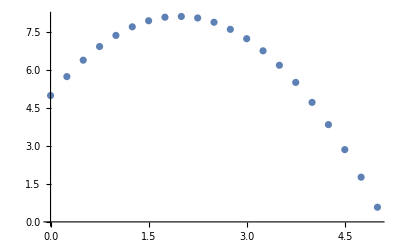

```mathematica
ListPlot[pontos]
```